```mathematica
SetDirectory["C:\\Users\\obser\\Documents\\Entropy and symmetry\\entropy-and-symmetry\\datasets\\Fractals with controlled parameter\\Space-Filling curves"]
```

C:\Users\obser\Documents\Entropy and symmetry\entropy-and-symmetry\datasets\Fractals with controlled parameter\Space-Filling curves

```mathematica
Unprotect@hilbertCurve; ClearAll@hilbertCurve;
hilbertCurve[1]=Line[{{0,0},{0,1},{1,1},{1,0}}];
hilbertCurve[n_]:=Line[(Reverse@(Round/@(RotationTransform[-90Degree,{(2^(n-1)-1)/2,(2^(n-1)-1)/2}]@Part[Level[hilbertCurve[n-1],1],1])))~Join~(TranslationTransform[{0,2^(n-1)}]/@(Round /@ Part[Level[hilbertCurve[n-1],1],1]))~Join~(TranslationTransform[{2^(n-1),2^(n-1)}]/@(Round /@ Part[Level[hilbertCurve[n-1],1],1]))~Join~(Reverse@(TranslationTransform[{2^(n-1),0}]/@(Round/@(RotationTransform[90Degree,{(2^(n-1)-1)/2,(2^(n-1)-1)/2}]@Part[Level[hilbertCurve[n-1],1],1]))))];
Protect@hilbertCurve;
```

{hilbertCurve1.png,hilbertCurve2.png,hilbertCurve3.png,hilbertCurve4.png,hilbertCurve5.png,hilbertCurve6.png,hilbertCurve7.png,hilbertCurve8.png}

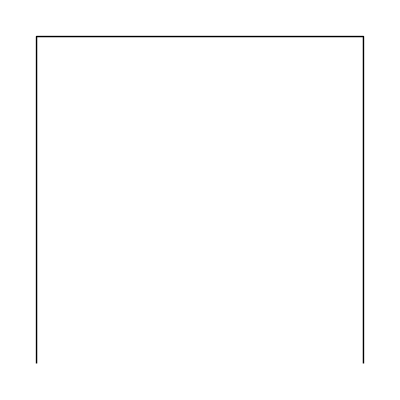
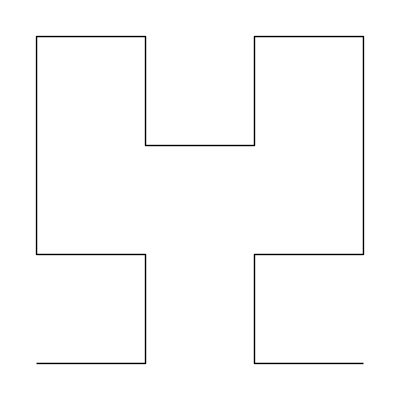
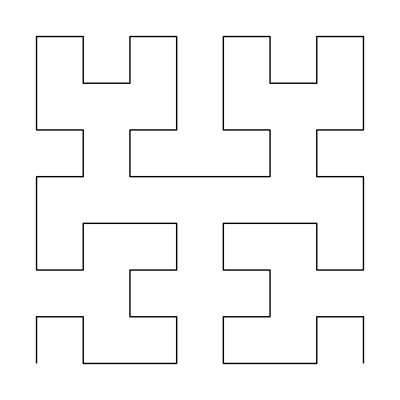
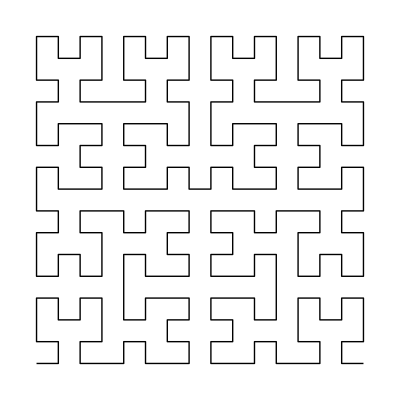
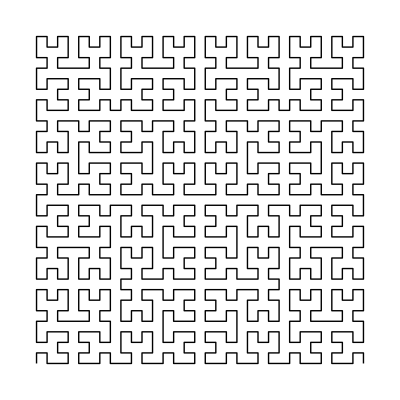
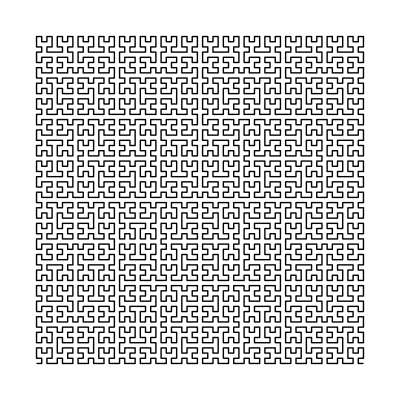
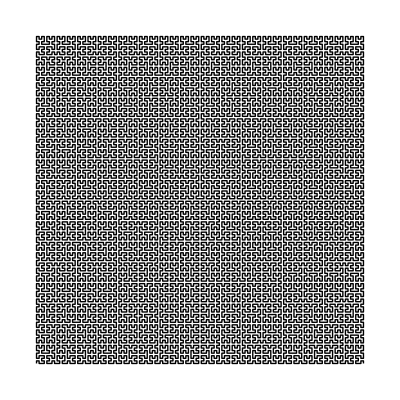
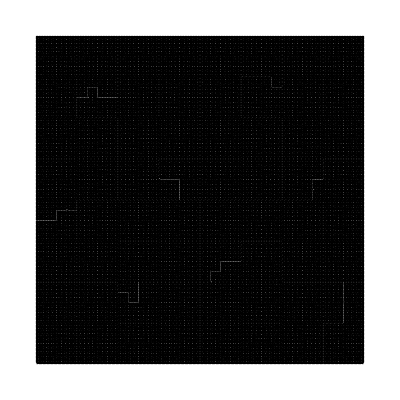

{hilbertCurve1.png,hilbertCurve2.png,hilbertCurve3.png,hilbertCurve4.png,hilbertCurve5.png,hilbertCurve6.png,hilbertCurve7.png,hilbertCurve8.png}

```mathematica
Table["hilbertCurve"<>ToString[i]<>".png",{i,8}]
Table[Graphics[hilbertCurve[i]],{i,8}]
Export@@@(Transpose@{%%,%})
```

```mathematica
SetDirectory["C:\\Users\\obser\\Documents\\Entropy and symmetry\\entropy-and-symmetry\\datasets\\Fractals with controlled parameter\\Line-Replacement Fractals"]
```

C:\Users\obser\Documents\Entropy and symmetry\entropy-and-symmetry\datasets\Fractals with controlled parameter\Line-Replacement Fractals

{KochSnowflake1.png,KochSnowflake2.png,KochSnowflake3.png,KochSnowflake4.png,KochSnowflake5.png,KochSnowflake6.png}

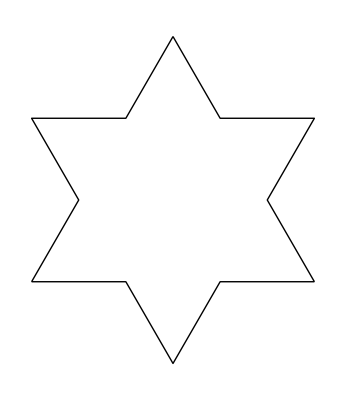
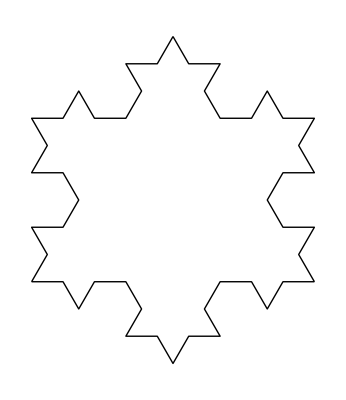
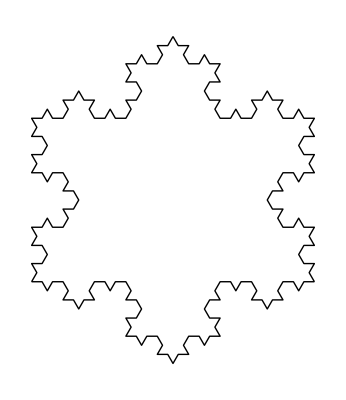
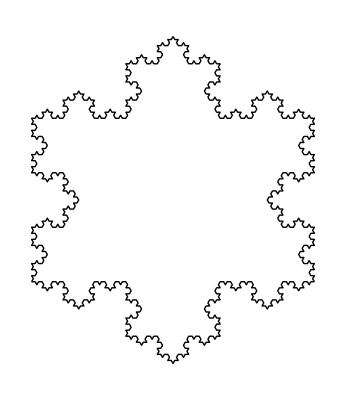
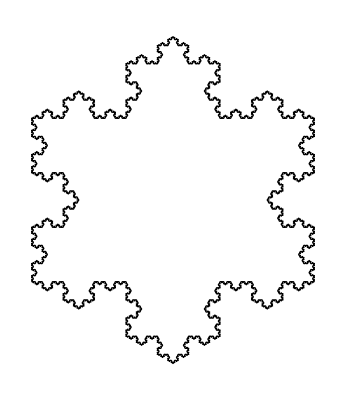
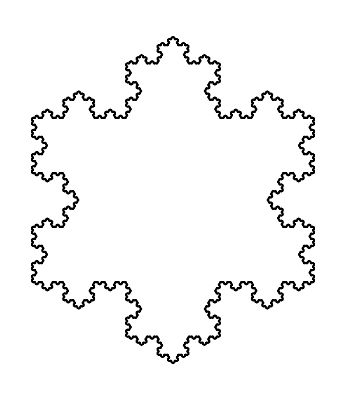

{KochSnowflake1.png,KochSnowflake2.png,KochSnowflake3.png,KochSnowflake4.png,KochSnowflake5.png,KochSnowflake6.png}

```mathematica
Table["KochSnowflake"<>ToString[i]<>".png",{i,6}]
Table[Graphics[GeometricTransformation[KochCurve[i],{RotationTransform[Pi,{1/2,0}],RotationTransform[-Pi/3,{1,0}],RotationTransform[Pi/3,{0,0}]}]],{i,6}]
Export@@@(Transpose@{%%,%})
```

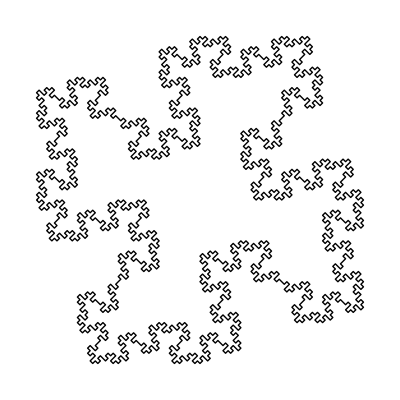

```mathematica
Graphics[ResourceFunction["MinkowskiSausageCurve"][Line[{{0,0},{1,1},{2,0},{1,-1},{0,0}}],3]]
```

{MinkowskiSausage1.png,MinkowskiSausage2.png,MinkowskiSausage3.png,MinkowskiSausage4.png}

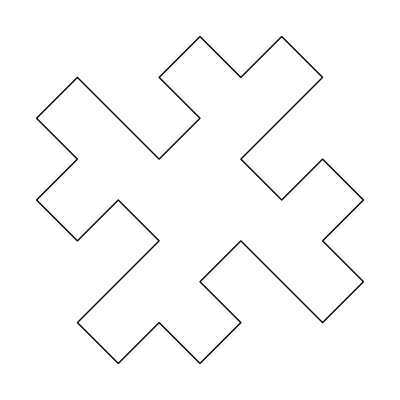
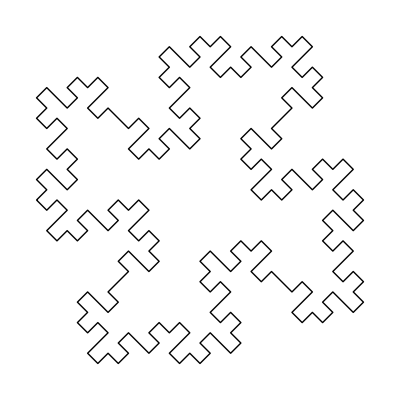
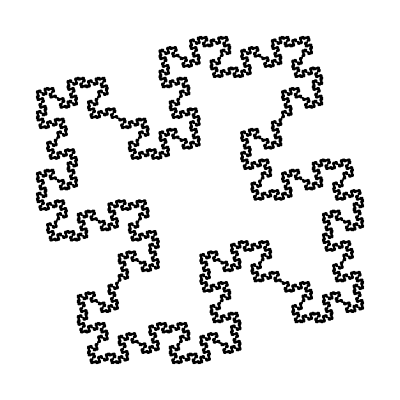
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{MinkowskiSausage1.png,MinkowskiSausage2.png,MinkowskiSausage3.png,MinkowskiSausage4.png}

```mathematica
Table["MinkowskiSausage"<>ToString[i]<>".png",{i,4}]
Table[Graphics[ResourceFunction["MinkowskiSausageCurve"][Line[{{0,0},{1,1},{2,0},{1,-1},{0,0}}],i]],{i,4}]
Export@@@(Transpose@{%%,%})
```

```mathematica
SetDirectory["C:\\Users\\obser\\Documents\\Entropy and symmetry\\entropy-and-symmetry\\datasets\\Fractals with controlled parameter\\Shape-Replacement Fractals"]
```

C:\Users\obser\Documents\Entropy and symmetry\entropy-and-symmetry\datasets\Fractals with controlled parameter\Shape-Replacement Fractals

{SierpinskiMesh1.png,SierpinskiMesh2.png,SierpinskiMesh3.png,SierpinskiMesh4.png,SierpinskiMesh5.png,SierpinskiMesh6.png}

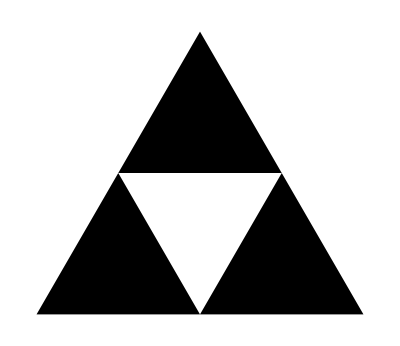
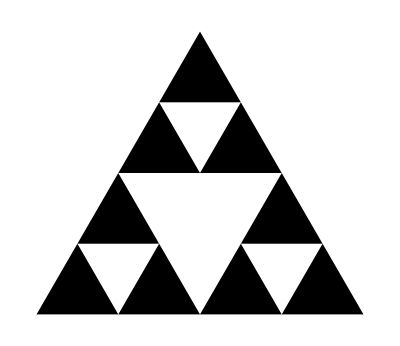
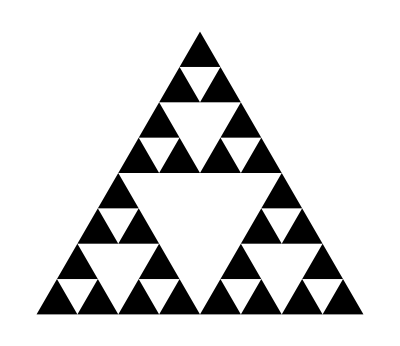
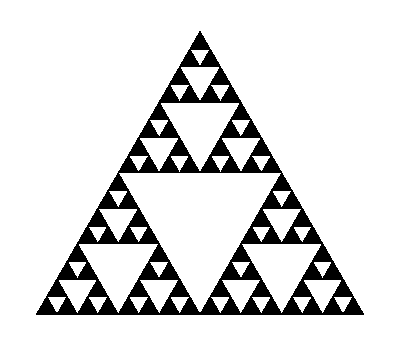
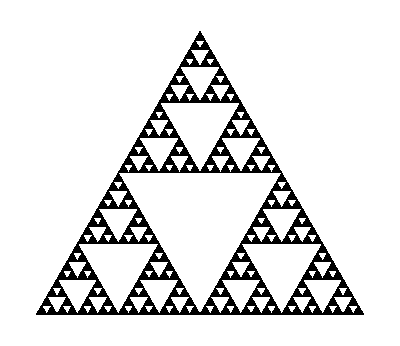
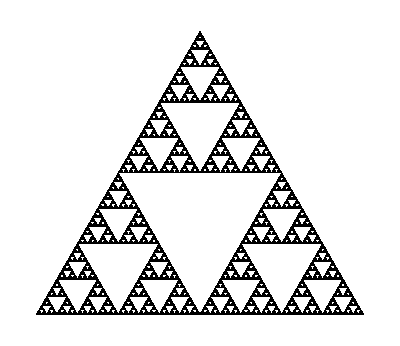

{SierpinskiMesh1.png,SierpinskiMesh2.png,SierpinskiMesh3.png,SierpinskiMesh4.png,SierpinskiMesh5.png,SierpinskiMesh6.png}

```mathematica
Table["SierpinskiMesh"<>ToString[i]<>".png",{i,6}]
Table[Graphics[SierpinskiMesh[i]],{i,6}]
Export@@@(Transpose@{%%,%})
```